```mathematica
SetDirectory[NotebookDirectory[]];
```

# h_scaling

## data

```mathematica
mpi=Flatten[Import["./mpi/buffer/mPion.dat"]];
```

```mathematica
fpi=Flatten[Import["./mub0/buffer/fpi.dat"]];
h=Flatten[Import["./mub0/buffer/c.dat"]]*197.33^3;
datamub0=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub0=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub0linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
fpi=Flatten[Import["./mub300/buffer/fpi.dat"]];
h=Flatten[Import["./mub300/buffer/c.dat"]]*197.33^3;
datamub300=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub300=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub300linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
fpi=Flatten[Import["./mub400/buffer/fpi.dat"]];
h=Flatten[Import["./mub400/buffer/c.dat"]]*197.33^3;
datamub400=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub400=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub400linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
fpi=Flatten[Import["./mub500/buffer/fpi.dat"]];
h=Flatten[Import["./mub500/buffer/c.dat"]]*197.33^3;
datamub500=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub500=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub500linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
fpi=Flatten[Import["./mub600/buffer/fpi.dat"]];
h=Flatten[Import["./mub600/buffer/c.dat"]]*197.33^3;
datamub600=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]]}];
h1mub600=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub600[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub600linear=Transpose[{mpi[[2;;Length[h]-2]],1/Flatten[Table[FindFit[datamub600[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
```

## Plot

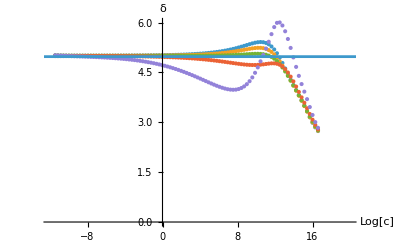

```mathematica
ploth=Show[ListPlot[{h1mub0,h1mub300,h1mub400,h1mub500,h1mub600},AxesLabel->{"Log[c]","δ"},PlotLegends->{(*"μ_B=0","μ_B=50MeV","μ_B=100MeV","μ_B=150MeV","μ_B=200MeV","μ_B=250MeV","μ_B=300MeV","μ_B=350MeV",*)(*"μ_B=400MeV","μ_B=450MeV","μ_B=500MeV","μ_B=550MeV"*)(*,"μ_B=600MeV","μ_B=650MeV","μ_B=700MeV"*)},Axes->True,PlotRange->{{-12,20},All}],ListLinePlot[{{-20,4.975},{100,4.975}}]]
```

```mathematica
Export["./LOdata/mub0.dat",h1mub0linear];
Export["./LOdata/mub300.dat",h1mub300linear];
Export["./LOdata/mub400.dat",h1mub400linear];
Export["./LOdata/mub500.dat",h1mub500linear];
Export["./LOdata/mub600.dat",h1mub600linear];
```